# SESION 4. LAB

## Parámetros

Constante de difusividad

```mathematica
α={0.1,0.3,0.6};
```

Número de nodos interiores (nodos de control)

```mathematica
NN={10,20,30};
```

Delta tiempo

```mathematica
dt={0.1,0.01,0.001};
```

Tiempo de horizonte

```mathematica
tf=80;
```

Número de pasos evolutivos

```mathematica
NumIt={IntegerPart[tf/dt[[1]] ],IntegerPart[tf/dt[[2]] ],IntegerPart[tf/dt[[3]] ] }
```

{800,8000,80000}

## Arreglos de almacenamiento

Utilizamos estos arreglos para almacenar los valores de u en cada tiempo del proceso t_s

```mathematica
MOD1=Array[mod1,NumIt[[1]]+1];MOD2=Array[mod2,NumIt[[2]]+1];MOD3=Array[mod3,NumIt[[3]]+1];MOD1B=Array[mod1,NumIt[[1]]+1];MOD2B=Array[mod2,NumIt[[2]]+1];MOD3B=Array[mod3,NumIt[[3]]+1];MOD1C=Array[mod1,NumIt[[1]]+1];MOD2C=Array[mod2,NumIt[[2]]+1];MOD3C=Array[mod3,NumIt[[3]]+1];
```

## Método diferencias finitas

### Matriz

Matriz de discretización espacial (derivada numérica)

```mathematica
An1=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{NN[[1]],NN[[1]]}];
```

```mathematica
An1//MatrixForm
```

(-2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | -2 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | -2 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | -2 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | -2 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | -2 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -2 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -2)

```mathematica
An1[[1,1]]=An1[[1,1]]+1;An1[[NN[[1]],NN[[1]]]]=An1[[NN[[1]],NN[[1]]]]+1;
```

```mathematica
An1//MatrixForm
```

(-1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | -2 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | -2 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | -2 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | -2 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | -2 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -2 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1)

### Condición inicial

Condición inicial

```mathematica
u0[x_]=x^2(1-x)^2;
```

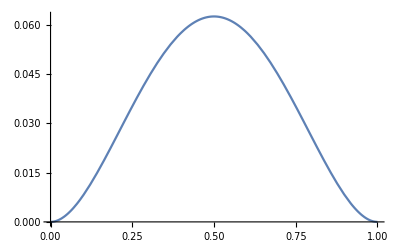

```mathematica
Plot[u0[x],{x,0,1}]
```

```mathematica
∫_0^1 u0[x]ⅆx
```

1/30

```mathematica
x0=0;t0=0
```

0

```mathematica
dx=(1-0)/(NN[[1]]+1);
```

```mathematica
UU0=Table[u0[x0+(k)*dx],{k,1,NN[[1]]}]//N
```

{0.00683013,0.0221296,0.0393416,0.0535483,0.0614712,0.0614712,0.0535483,0.0393416,0.0221296,0.00683013}

### Término no homogéneo

```mathematica
ff[x_,t_]=Exp[-2*t]*Cos[x*Pi];
```

```mathematica
FF=Table[ff[x0+(k)*dx,t0+(k)*dt[[1]]],{k,1,NN[[1]]}]//N
```

{0.785566,0.563909,0.359395,0.186658,0.0523547,-0.0428644,-0.10244,-0.132214,-0.139058,-0.129853}

## Metodología

### Caso 1 (Método de Euler Explícito)

```mathematica
TT=IdentityMatrix[NN[[1]]]+α[[1]]*dt[[1]]*An1;
```

```mathematica
Eigenvalues[TT]
```

{1.,0.999021,0.99618,0.991756,0.98618,0.98,0.97382,0.968244,0.96382,0.960979}

```mathematica
Eigensystem[TT]
```

{{1.,0.999021,0.99618,0.991756,0.98618,0.98,0.97382,0.968244,0.96382,0.960979},{{0.316228,0.316228,0.316228,0.316228,0.316228,0.316228,0.316228,0.316228,0.316228,0.316228},{-0.441708,-0.39847,-0.316228,-0.203031,-0.0699596,0.0699596,0.203031,0.316228,0.39847,0.441708},{0.425325,0.262866,-5.92799×10^-16,-0.262866,-0.425325,-0.425325,-0.262866,3.19199×10^-16,0.262866,0.425325},{0.39847,0.0699596,-0.316228,-0.441708,-0.203031,0.203031,0.441708,0.316228,-0.0699596,-0.39847},{-0.361803,0.138197,0.447214,0.138197,-0.361803,-0.361803,0.138197,0.447214,0.138197,-0.361803},{-0.316228,0.316228,0.316228,-0.316228,-0.316228,0.316228,0.316228,-0.316228,-0.316228,0.316228},{-0.262866,0.425325,1.77077×10^-15,-0.425325,0.262866,0.262866,-0.425325,1.03295×10^-15,0.425325,-0.262866},{-0.203031,0.441708,-0.316228,-0.0699596,0.39847,-0.39847,0.0699596,0.316228,-0.441708,0.203031},{0.138197,-0.361803,0.447214,-0.361803,0.138197,0.138197,-0.361803,0.447214,-0.361803,0.138197},{-0.0699596,0.203031,-0.316228,0.39847,-0.441708,0.441708,-0.39847,0.316228,-0.203031,0.0699596}}}

```mathematica
NumIt[[1]]
```

800

```mathematica
Eigenvalues[TT^100]
```

{0.366032,0.366032,0.13262,0.13262,0.13262,0.13262,0.13262,0.13262,0.13262,0.13262}

### Caso 2 (Método de Euler Implícito)

```mathematica
BB=IdentityMatrix[NN[[1]]]-α[[1]]*dt[[1]]*An1;
```

```mathematica
Eigenvalues[BB]
```

{1.03902,1.03618,1.03176,1.02618,1.02,1.01382,1.00824,1.00382,1.00098,1.}

```mathematica
TTEI=Inverse[BB];
```

```mathematica
Eigenvalues[TTEI]
```

{1.,0.999022,0.996195,0.991823,0.986369,0.980392,0.974488,0.969222,0.965083,0.962444}

```mathematica
Eigensystem[TTEI]
```

{{1.,0.999022,0.996195,0.991823,0.986369,0.980392,0.974488,0.969222,0.965083,0.962444},{{-0.316228,-0.316228,-0.316228,-0.316228,-0.316228,-0.316228,-0.316228,-0.316228,-0.316228,-0.316228},{-0.441708,-0.39847,-0.316228,-0.203031,-0.0699596,0.0699596,0.203031,0.316228,0.39847,0.441708},{0.425325,0.262866,1.58848×10^-14,-0.262866,-0.425325,-0.425325,-0.262866,2.06396×10^-15,0.262866,0.425325},{0.39847,0.0699596,-0.316228,-0.441708,-0.203031,0.203031,0.441708,0.316228,-0.0699596,-0.39847},{0.361803,-0.138197,-0.447214,-0.138197,0.361803,0.361803,-0.138197,-0.447214,-0.138197,0.361803},{-0.316228,0.316228,0.316228,-0.316228,-0.316228,0.316228,0.316228,-0.316228,-0.316228,0.316228},{-0.262866,0.425325,1.59537×10^-14,-0.425325,0.262866,0.262866,-0.425325,-5.80205×10^-15,0.425325,-0.262866},{-0.203031,0.441708,-0.316228,-0.0699596,0.39847,-0.39847,0.0699596,0.316228,-0.441708,0.203031},{-0.138197,0.361803,-0.447214,0.361803,-0.138197,-0.138197,0.361803,-0.447214,0.361803,-0.138197},{0.0699596,-0.203031,0.316228,-0.39847,0.441708,-0.441708,0.39847,-0.316228,0.203031,-0.0699596}}}

```mathematica
NumIt[[1]]
```

800

```mathematica
Eigenvalues[TTEI^100]
```

{0.373318,0.373318,0.140726,0.140726,0.140713,0.140713,0.140713,0.140713,0.140713,0.140713}

### Caso 3 (Método de Crank-Nicolson)

```mathematica
BBI=IdentityMatrix[NN[[1]]]-1/2 α[[1]]*dt[[1]]*An1;BBE=IdentityMatrix[NN[[1]]]+1/2 α[[1]]*dt[[1]]*An1;
```

```mathematica
Eigenvalues[BBI]
```

{1.01951,1.01809,1.01588,1.01309,1.01,1.00691,1.00412,1.00191,1.00049,1.}

```mathematica
Eigenvalues[BBE]
```

{1.,0.999511,0.99809,0.995878,0.99309,0.99,0.98691,0.984122,0.98191,0.980489}

```mathematica
BBIN=Inverse[BBI];
```

```mathematica
TTCN=BBIN.BBE;
```

```mathematica
Eigenvalues[TTCN]
```

{1.,0.999022,0.996188,0.99179,0.986275,0.980198,0.974158,0.968741,0.964463,0.961726}

```mathematica
Eigensystem[TTCN]
```

{{1.,0.999022,0.996188,0.99179,0.986275,0.980198,0.974158,0.968741,0.964463,0.961726},{{-0.316228,-0.316228,-0.316228,-0.316228,-0.316228,-0.316228,-0.316228,-0.316228,-0.316228,-0.316228},{-0.441708,-0.39847,-0.316228,-0.203031,-0.0699596,0.0699596,0.203031,0.316228,0.39847,0.441708},{0.425325,0.262866,1.12054×10^-14,-0.262866,-0.425325,-0.425325,-0.262866,1.29237×10^-14,0.262866,0.425325},{0.39847,0.0699596,-0.316228,-0.441708,-0.203031,0.203031,0.441708,0.316228,-0.0699596,-0.39847},{0.361803,-0.138197,-0.447214,-0.138197,0.361803,0.361803,-0.138197,-0.447214,-0.138197,0.361803},{-0.316228,0.316228,0.316228,-0.316228,-0.316228,0.316228,0.316228,-0.316228,-0.316228,0.316228},{-0.262866,0.425325,1.79214×10^-15,-0.425325,0.262866,0.262866,-0.425325,2.09361×10^-14,0.425325,-0.262866},{0.203031,-0.441708,0.316228,0.0699596,-0.39847,0.39847,-0.0699596,-0.316228,0.441708,-0.203031},{-0.138197,0.361803,-0.447214,0.361803,-0.138197,-0.138197,0.361803,-0.447214,0.361803,-0.138197},{0.0699596,-0.203031,0.316228,-0.39847,0.441708,-0.441708,0.39847,-0.316228,0.203031,-0.0699596}}}

```mathematica
NumIt[[1]]
```

800

```mathematica
Eigenvalues[TTEI^100]
```

{0.373318,0.373318,0.140726,0.140726,0.140713,0.140713,0.140713,0.140713,0.140713,0.140713}

## Implementación

### Caso Euler Explícito

Construcción de las aproximaciones para cada uno de los estados evolutivos

```mathematica
MOD1[[1]]=UU0
```

{0.00683013,0.0221296,0.0393416,0.0535483,0.0614712,0.0614712,0.0535483,0.0393416,0.0221296,0.00683013}

```mathematica
TT.MOD1[[1]]+FF[[1]]
```

{0.79255,0.807715,0.824878,0.839052,0.846958,0.846958,0.839052,0.824878,0.807715,0.79255}

```mathematica
TT.MOD1[[1]]
```

{0.00698313,0.0221488,0.0393115,0.0534854,0.061392,0.061392,0.0534854,0.0393115,0.0221488,0.00698313}

```mathematica
dt
```

{0.1,0.01,0.001}

```mathematica
For[i=2,i<=NumIt[[1]]+1,i++,MOD1[[i]]=TT.MOD1[[i-1]]+dt[[1]] FF]
```

```mathematica
MOD1[[3]]
```

{0.164026,0.134968,0.111192,0.0907928,0.0718229,0.0527757,0.0329645,0.0128617,-0.00562687,-0.0188451}

```mathematica
{0.007134785875281742,0.022168731644013385,0.03928163376818523,0.053422744348063655,0.06131291578444095,0.06131291578444095,0.053422744348063655,0.03928163376818523,0.022168731644013385,0.007134785875281742}
```

{0.00713479,0.0221687,0.0392816,0.0534227,0.0613129,0.0613129,0.0534227,0.0392816,0.0221687,0.00713479}

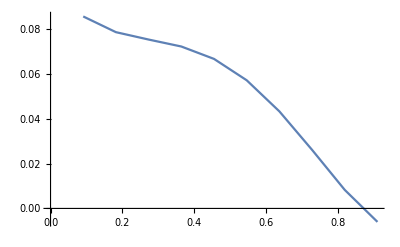

```mathematica
ListLinePlot[Table[{j*dx,MOD1[[2]][[j]]},{j,1,NN[[1]]}]]
```

```mathematica
NumIt[[1]]
```

800

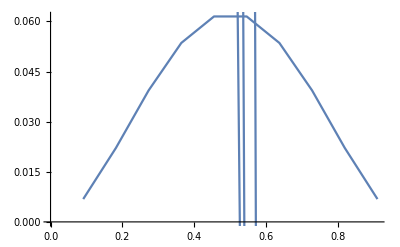

```mathematica
Show[{ListLinePlot[Table[{j*dx,MOD1[[1]][[j]]},{j,1,NN[[1]]}]],ListLinePlot[Table[{j*dx,MOD1[[100]][[j]]},{j,1,NN[[1]]}]],ListLinePlot[Table[{j*dx,MOD1[[200]][[j]]},{j,1,NN[[1]]}]],ListLinePlot[Table[{j*dx,MOD1[[400]][[j]]},{j,1,NN[[1]]}]]}]
```

```mathematica
NumIt[[1]]
```

800

```mathematica
Manipulate[ListLinePlot[Table[{j*dx,MOD1[[k]][[j]]},{j,1,NN[[1]]}],PlotRange->{0,4},Frame->True,PlotLabel->NumberForm[dt[[1]]*k],PlotStyle->{Hue[0.1*k/tf]}],{k,2,NumIt[[1]],5}]
```

(Valor promedio)

```mathematica
NIntegrate[u0[x],{x,0,1}]/1
```

0.0333333

### Caso Euler Implícito

Construcción de las aproximaciones para cada uno de los estados evolutivos

```mathematica
MOD1B[[1]]=UU0
```

{0.00683013,0.0221296,0.0393416,0.0535483,0.0614712,0.0614712,0.0535483,0.0393416,0.0221296,0.00683013}

```mathematica
For[i=2,i<=NumIt[[1]]+1,i++,MOD1B[[i]]=TTEI.MOD1B[[i-1]]+dt[[1]]TTEI.FF]
```

```mathematica
MOD1B[[3]]
```

{0.16359,0.134995,0.111256,0.0908697,0.0719013,0.0528472,0.0330244,0.0129079,-0.0055939,-0.0188651}

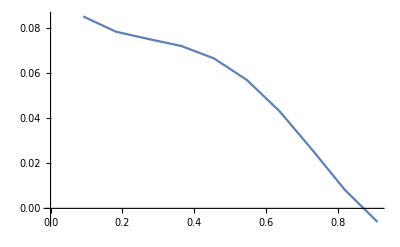

```mathematica
ListLinePlot[Table[{j*dx,MOD1B[[2]][[j]]},{j,1,NN[[1]]}]]
```

```mathematica
NumIt[[1]]
```

800

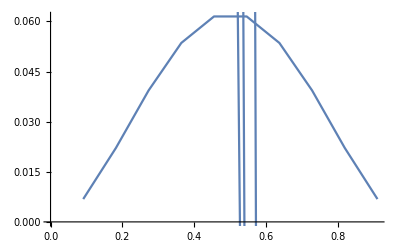

```mathematica
Show[{ListLinePlot[Table[{j*dx,MOD1B[[1]][[j]]},{j,1,NN[[1]]}]],ListLinePlot[Table[{j*dx,MOD1B[[100]][[j]]},{j,1,NN[[1]]}]],ListLinePlot[Table[{j*dx,MOD1B[[200]][[j]]},{j,1,NN[[1]]}]],ListLinePlot[Table[{j*dx,MOD1B[[400]][[j]]},{j,1,NN[[1]]}]]}]
```

```mathematica
NumIt[[1]]
```

800

```mathematica
Manipulate[ListLinePlot[Table[{j*dx,MOD1B[[k]][[j]]},{j,1,NN[[1]]}],PlotRange->{0,4},Frame->True,PlotLabel->NumberForm[dt[[1]]*k],PlotStyle->{Hue[0.1*k/tf]}],{k,2,NumIt[[1]],5}]
```

(Valor promedio)

```mathematica
NIntegrate[u0[x],{x,0,1}]/1
```

0.0333333

### Caso Crank-Nicolson

Construcción de las aproximaciones para cada uno de los estados evolutivos

```mathematica
MOD1C[[1]]=UU0
```

{0.00683013,0.0221296,0.0393416,0.0535483,0.0614712,0.0614712,0.0535483,0.0393416,0.0221296,0.00683013}

```mathematica
For[i=2,i<=NumIt[[1]]+1,i++,MOD1C[[i]]=TTCN.MOD1C[[i-1]]+dt[[1]]BBIN.FF]
```

```mathematica
MOD1B[[3]]
```

{0.16359,0.134995,0.111256,0.0908697,0.0719013,0.0528472,0.0330244,0.0129079,-0.0055939,-0.0188651}

```mathematica
ListLinePlot[Table[{j*dx,MOD1B[[2]][[j]]},{j,1,NN[[1]]}]]
```

-Graphics-

```mathematica
NumIt[[1]]
```

800

```mathematica
Show[{ListLinePlot[Table[{j*dx,MOD1B[[1]][[j]]},{j,1,NN[[1]]}]],ListLinePlot[Table[{j*dx,MOD1B[[100]][[j]]},{j,1,NN[[1]]}]],ListLinePlot[Table[{j*dx,MOD1B[[200]][[j]]},{j,1,NN[[1]]}]],ListLinePlot[Table[{j*dx,MOD1B[[400]][[j]]},{j,1,NN[[1]]}]]}]
```

-Graphics-

```mathematica
NumIt[[1]]
```

800

```mathematica
Manipulate[ListLinePlot[Table[{j*dx,MOD1C[[k]][[j]]},{j,1,NN[[1]]}],PlotRange->{0,4},Frame->True,PlotLabel->NumberForm[dt[[1]]*k],PlotStyle->{Hue[0.1*k/tf]}],{k,2,NumIt[[1]],5}]
```

Part::partw: Part 2 of mod1[277] does not exist.

Part::partw: Part 3 of mod1[277] does not exist.

Part::partw: Part 4 of mod1[277] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 2 of mod1[277] does not exist.

Part::partw: Part 3 of mod1[277] does not exist.

Part::partw: Part 4 of mod1[277] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 2 of mod1[2] does not exist.

Part::partw: Part 3 of mod1[2] does not exist.

Part::partw: Part 4 of mod1[2] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

(Valor promedio)

```mathematica
NIntegrate[u0[x],{x,0,1}]/1
```

0.0333333

## Runge-Kutta

```mathematica
MOD1RK4=Array[mod1rk,NumIt[[1]]+1];
```

```mathematica
FRK4[AA_,vec1_,vec2_,dd_]:=Module[{v1},v1=dd*AA.vec1+0.5*vec2;v1]
```

```mathematica
par=dt[[1]]
```

0.1

```mathematica
MARK4=α[[1]]An1;
```

```mathematica
UU0;
```

```mathematica
KK1=par*FRK4[MARK4,UU0,UU0,0];
```

```mathematica
KK2=par*FRK4[MARK4,UU0,KK1,par];
```

```mathematica
KK3=par*FRK4[MARK4,UU0,KK2,par];
```

```mathematica
KK4=par*FRK4[MARK4,UU0,KK3,2*par];
```

```mathematica
UU1=UU0 +1/6*(KK1+2*KK2+2*KK3+KK4)
```

{0.00690872,0.0223354,0.0397008,0.054035,0.0620292,0.0620292,0.054035,0.0397008,0.0223354,0.00690872}

```mathematica
MODRK4[AA_,vec1_,dd_]:=Module[{v1,kk1,kk2,kk3,kk4},kk1=dd*FRK4[AA,vec1,vec1,0];kk2=dd*FRK4[AA,vec1,kk1,dd];kk3=dd*FRK4[AA,vec1,kk2,dd];kk4=dd*FRK4[AA,vec1,kk3,2*dd];v1=1/6*(kk1+2*(kk2+kk3)+kk4)]
```

```mathematica
MODRK4[MARK4,UU0,par]
```

{0.0000785896,0.000205761,0.00035923,0.000486703,0.000557987,0.000557987,0.000486703,0.00035923,0.000205761,0.0000785896}

```mathematica
MOD1RK4[[1]]=UU0;
```

```mathematica
For[i=2,i≤NumIt[[1]]+1,i++,MOD1RK4[[i]]=MOD1RK4]
```